```mathematica
n=199;
der=Table[
First@Import["I:\\Ikabur\\gos\\tmp\\"<>IntegerString[i,10,3]<>"_001_derivative.csv"],
{i,n}];
state=Table[
First@Import["I:\\Ikabur\\gos\\tmp\\"<>IntegerString[i,10,3]<>"_001_state.csv"],
{i,n}];
```

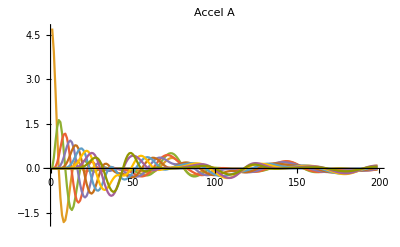

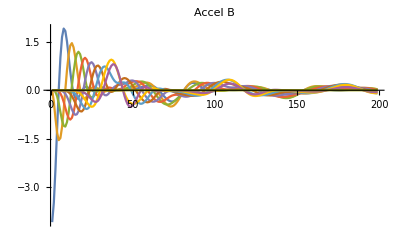

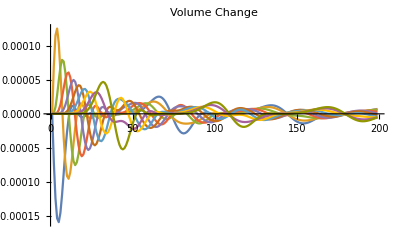

```mathematica
derVelA=Table[der[[All,k]],{k,1,30,3}];
derVelB=Table[der[[All,k]],{k,2,30,3}];
derVol=Table[der[[All,k]],{k,3,30,3}];
ListPlot[derVelA,Joined->True,PlotRange->All,PlotLabel->"Accel A"]
ListPlot[derVelB,Joined->True,PlotRange->All,PlotLabel->"Accel B"]
ListPlot[derVol,Joined->True,PlotRange->All,PlotLabel->"Volume Change"]
```

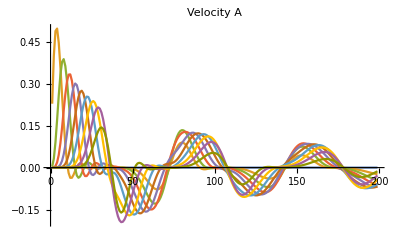

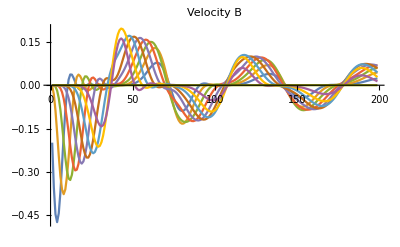

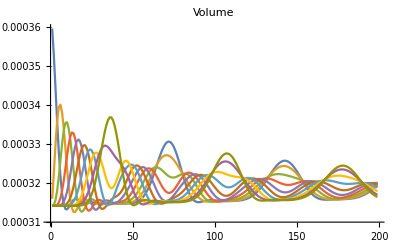

```mathematica
stateVelA=Table[state[[All,k]],{k,1,30,3}];
stateVelB=Table[state[[All,k]],{k,2,30,3}];
stateVol=Table[state[[All,k]],{k,3,30,3}];
ListPlot[stateVelA,Joined->True,PlotRange->All,PlotLabel->"Velocity A"]
ListPlot[stateVelB,Joined->True,PlotRange->All,PlotLabel->"Velocity B"]
ListPlot[stateVol,Joined->True,PlotRange->All, PlotLabel->"Volume"]
```

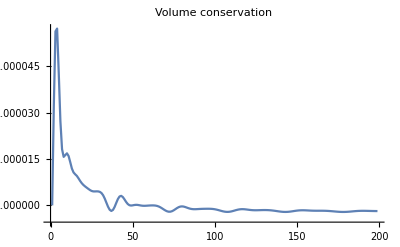

```mathematica
totalVol=Total/@Transpose@stateVol;
ListPlot[totalVol/totalVol[[1]],Joined->True,PlotRange->All,PlotLabel->"Volume conservation"]
```

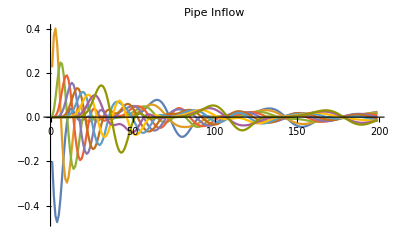

```mathematica
ListPlot[stateVelA+stateVelB,Joined->True,PlotRange->All,PlotLabel->"Pipe Inflow"]
```

```mathematica
through[x_,y_]:=
```

```mathematica
volumeToRadius[v_]:=With[{L=1,n=1},√(v/(π L n))]
```

```mathematica
Clear[plotPipes]
plotPipes[radii_List,r0_List,length_]:=Graphics[Table[
With[{r=1+20(radii[[i]]/r0[[i]]-1)},
Rectangle[{i length,-r},{(i+1) length,r}]
],
{i,Length@radii}],
PlotRange->{{0,Length@radii length},{-2,2}}
]
With[{u=Transpose[volumeToRadius/@stateVol]},
Manipulate[plotPipes[u[[i]],Table[0.01,{i,10}],1],{i,1,Length@u,1}
]]
```

```mathematica
frames=With[{u=Transpose[volumeToRadius/@stateVol]},
Table[plotPipes[u[[i]],Table[0.01,{i,10}],1],{i,1,Length@u}]];
Export["I:/Ikabur/gos/tmp/pipechain.gif",frames,"DisplayOptions"->0.05]
```

I:/Ikabur/gos/tmp/pipechain.gif